```mathematica
ϵ (Log[ϵ]-Log[1/(n+1)])+(1-ϵ)(Log[(1-ϵ)/n]-Log[1/(n+1)])
```

(1-ϵ) (-Log[1/(1+n)]+Log[(1-ϵ)/n])+ϵ (-Log[1/(1+n)]+Log[ϵ])

```mathematica
%//Simplify
```

-Log[1/(1+n)]-(-1+ϵ) Log[(1-ϵ)/n]+ϵ Log[ϵ]

```mathematica
Dkl = %
```

-Log[1/(1+n)]-(-1+ϵ) Log[(1-ϵ)/n]+ϵ Log[ϵ]

```mathematica
Dkl/.ϵ->1/(n+1)
```

-Log[1/(1+n)]+Log[1/(1+n)]/(1+n)-(-1+1/(1+n)) Log[(1-1/(1+n))/n]

```mathematica
%//Simplify
```

0

```mathematica
Dkl
```

-Log[1/(1+n)]-(-1+ϵ) Log[(1-ϵ)/n]+ϵ Log[ϵ]

```mathematica
%/.ϵ->1/n^2
```

Log[1/n^2]/n^2-(-1+1/n^2) Log[(1-1/n^2)/n]-Log[1/(1+n)]

```mathematica
%//Simplify
```

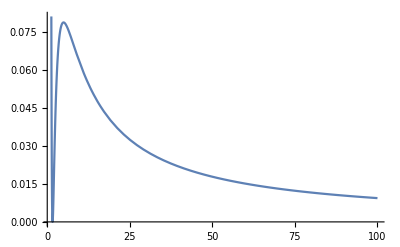

```mathematica
Plot[%,{n,1,100}]
```

```mathematica
Simplify[Log[1/n^2]/n^2-(-1+1/n^2) Log[(1-1/n^2)/n]-Log[1/(1+n)], Assumptions->n>1]
```

Log[((-1+n) (1+n)^2)/n^3]+Log[n/(-1+n^2)]/n^2

```mathematica
Series[%,{n,Infinity,2}]
```

1/n+(-3-2 Log[n])/(2 n^2)+O[1/n]^3

```mathematica
w
```